## Load Data

```mathematica
ClearAll["Global`*"]
mydata=Import[StringJoin[NotebookDirectory[],"data/ExampleFreezeOutCorrected.csv"]];
headers=mydata[[1]]
fields=Transpose@mydata[[2;;]];
αs=fields[[1]];
τs=fields[[2]];
rs=fields[[3]];
Dτs=fields[[4]];
Drs=fields[[5]];
urs=fields[[6]];
uτs=fields[[7]];
```

{alpha,tau,r,Dtau,Dr,ur,utau}

```mathematica
ur=Interpolation[Transpose@{αs,urs}];
uτ=Interpolation[Transpose@{αs,uτs}];
r=Interpolation[Transpose@{αs,rs}];
Dr=Interpolation[Transpose@{αs,Drs}];
τ=Interpolation[Transpose@{αs,τs}];
Dτ=Interpolation[Transpose@{αs,Dτs}];
```

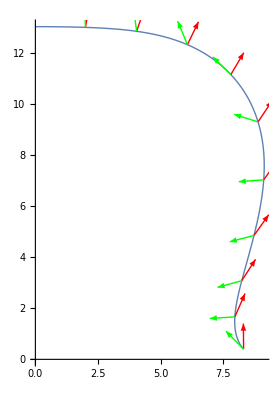

```mathematica
u[α_]=1/Sqrt[ur[α]^2+uτ[α]^2]*{ur[α],uτ[α]};
n[α_]=1/Sqrt[Dτ[α]^2+Dr[α]^2]*{Dτ[α],Dr[α]};
curve[α_]:={r[α],τ[α]};
ParametricPlot[
curve[α],{α,0,π/2},PlotStyle->Thick,
Epilog->{
{
Red,Thick,Arrow[{curve@#,curve@#+u@#}]&/@Rest[Subdivide[0,Pi/2,10]]
},
{
Green,Thick,Arrow[{curve@#,curve@#+n@#}]&/@Rest[Subdivide[0,Pi/2,10]]
}},
PlotRange->Automatic]
```

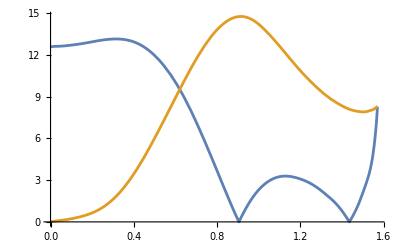

```mathematica
Plot[{Abs@Dr[x],Abs@Dτ[x]},{x,0,π/2}]
```

## Compute Initial Fields

For all scenarios, ϵ can be a reference scale, using

ϵ=1/2 m^2 ϕ_R^2+1/2(∂_μ ϕ_R)(∂^μ ϕ_R)
ϵ=m^2 ϕ_C^2+(∂_μ ϕ_C)(∂^μ ϕ_C)

```mathematica
GeVtoIfm=5.0677;(*5.0677;(*1GeV=5.0677(fm^-1)\[hbar]c*)*)
IfmtoGeV=1/GeVtoIfm;
fmtoIGeV=GeVtoIfm;
IGeVtofm=1/fmtoIGeV;
ϵ=0.1*0.160054*IfmtoGeV^3;(*energy density at freeze out in GeV/(fm^3)*)
```

### A) Constant Real Fields

#### A1) Fixed Mass, Varying Ratio of (Amplitude/Derivative)

Not saved!

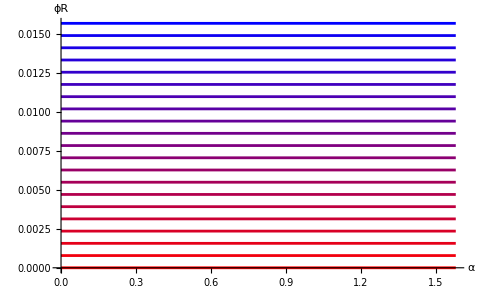

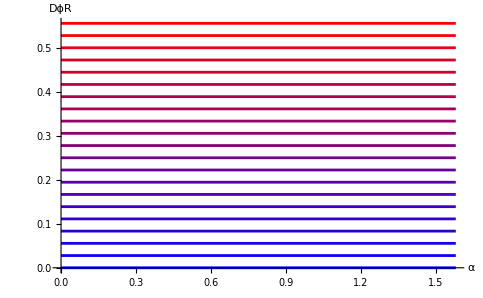

```mathematica
save=False;
If[save,Print["Saved!"],Print["Not saved!"]]

m=1000;(*MeV*)
ϕmax=Sqrt[2*ϵ]/(m/1000);
Dϕmax=7*fmtoIGeV*Sqrt[2*ϵ];(*Since Dϕ~dx^μ/dα∂_μ ϕ anddx^μ/dα~(10fm)/(π/2)~7fm *)
sign=1;

description="constfield_fixedm"<>ToString[m];
timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];

plotsϕ={};
plotsDϕ={};

nsteps=21;
Do[
t=N@(i-1)/(nsteps-1);

ϕ=(1-t)*ϕmax;
Dϕ=sign*t*Dϕmax;

AppendTo[plotsϕ,ListLinePlot[ {{0.0,ϕ},{π/2+0.01,ϕ}}, AxesLabel -> {α, ϕR},PlotStyle->Blend[{Blue,Red},t]]];
AppendTo[plotsDϕ,ListLinePlot[ {{0.0,Dϕ},{π/2+0.01,Dϕ}}, AxesLabel -> {α, DϕR},PlotStyle->Blend[{Blue,Red},t]]];

initdata = {{0.0,ϕ,0,Dϕ,0},{π/2+0.01,ϕ,0,Dϕ,0}};
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# "<>timestamp<>"\n# epsilon:" <> ToString[ϵ] <> "(GeV^4)\n# mass:" <> ToString[m/1000]<>"(GeV)\n# sign:"<>ToString[sign]}];
If[save,Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/init_real_"<>description<>"_"<>timestamp<>"/init"<>IntegerString[i-1,10,Ceiling[Log10[nsteps]]]<>".csv"],table,"Table","FieldSeparators"->","],];
,{i,nsteps}]

Show[plotsϕ,PlotRange->All]
Show[plotsDϕ,PlotRange->All]

Clear[save,m,ϕmax,Dϕmax,sign,description,timestamp,plotsϕ,plotsDϕ,nsteps,t,ϕ,Dϕ,initdata,table]
```

### B) Real Field with Constant Energy Density

#### B1) Fixed Mass, Varying Ratio of ϵpot/ϵkin

Not saved!

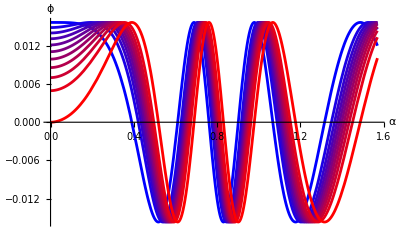

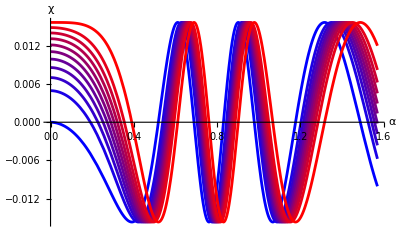

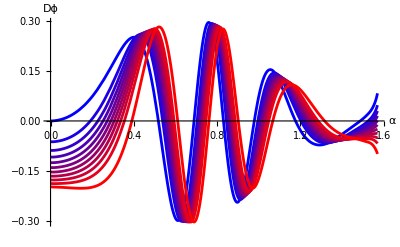

```mathematica
save=False;
If[save,Print["Saved!"],Print["Not saved!"]]

m=1000;(*MeV*)
sign=1;

description="consteps_fixedm"<>ToString[Mass];
timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];

plotsϕ={};
plotsχ={};
plotsDϕ={};

nsteps=11;
Do[
ratio=N@(i-1)/(nsteps-1);

ϵpot=(1-ratio)*ϵ;
ϵkin=ratio*ϵ;

ϕ0=Sqrt[2*ϵpot]/(m/1000);
χ0=sign*Sqrt[2*ϵkin];

ODEs = {
      ϕODE'[α] == χODE[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α]),
      χODE'[α] == -(m/1000)^2*ϕODE[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α])};
ICs = {ϕODE[0] == ϕ0, χODE[0] == χ0};
solution = NDSolve[{ODEs, ICs}, {ϕODE[α], χODE[α]}, {α, 0, Pi/2}];

ϕ[t_] := (ϕODE[α] /. solution[[1]] /. α -> t);
χ[t_] := (χODE[α] /. solution[[1]] /. α -> t);
Dϕ[t_] := (-Dr[t]*uτ[t] + Dτ[t]*ur[t])*χ[t];

AppendTo[plotsϕ,Plot[ϕ[x], {x, 0, Pi/2}, AxesLabel -> {α, ϕ},PlotStyle->Blend[{Blue,Red},ratio]]];
AppendTo[plotsχ,Plot[χ[x], {x, 0, Pi/2}, AxesLabel -> {α, χ},PlotStyle->Blend[{Blue,Red},ratio]]];
AppendTo[plotsDϕ,Plot[Dϕ[x], {x, 0, Pi/2}, AxesLabel -> {α, Dϕ},PlotStyle->Blend[{Blue,Red},ratio]]];

initdata = Table[{α, Re@ϕRfunc[α], Im@ϕRfunc[α], Re@DϕRfunc[α], Im@DϕRfunc[α]}, {α, 0, Pi/2 + 0.01, .01}];

initdata = Table[{α, Re@ϕRfunc[α], Im@ϕRfunc[α], Re@DϕRfunc[α], Im@DϕRfunc[α]}, {α, 0, Pi/2 + 0.01, .01}];
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# "<>timestamp<>"\n# epsilon:" <> ToString[ϵ] <> "(GeV^4)\n# mass:" <> ToString[m/1000]<>"(GeV)\n# sign:"<>ToString[sign]}];
If[save,Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/init_real_"<>description<>"_"<>timestamp<>"/init"<>IntegerString[i-1,10,Ceiling[Log10[nsteps]]]<>".csv"],table,"Table","FieldSeparators"->","],];
,{i,nsteps}]

Show[plotsϕ,PlotRange->All]
Show[plotsχ,PlotRange->All]
Show[plotsDϕ,PlotRange->All]

Clear[save,m,sign,description,timestamp,plotsϕ,plotsχ,plotsDϕ,nsteps,ratio,ϵpot,ϵkin,ϕ0,χ0,ODEs,ICs,solution,ϕ,χ,Dϕ,initdata,table]
```

#### B2) Fixed Ratio of ϵpot/ϵkin , varying Mass

Saved!

InterpolatingFunction::dmval: Input value {1.58} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

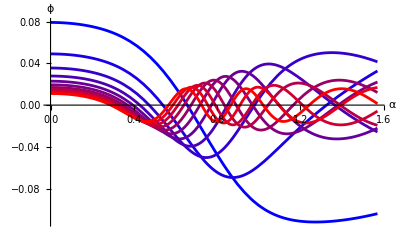

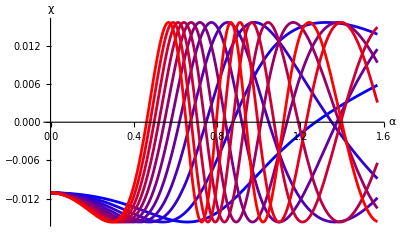

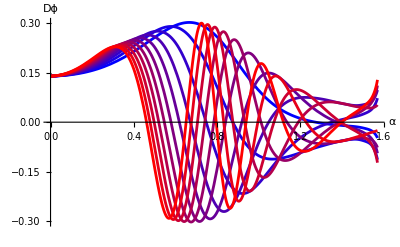

```mathematica
save=False;
If[save,Print["Saved!"],Print["Not saved!"]]

mmin=140;(*MeV*)
mmax=1000;(*MeV*)
sign=1;
ratio=0.5;
ϵpot=(1-ratio)*ϵ;
ϵkin=ratio*ϵ;

description="consteps_varm";
timestamp = Block[{$DateStringFormat = {"Year", "Month", "Day", "_", "Hour", "Minute", "Second"}}, DateString[]];

plotsϕ={};
plotsχ={};
plotsDϕ={};

nsteps=11;
Do[
t=N@(i-1)/(nsteps-1);
m=mmin+t*(mmax-mmin);

ϕ0=Sqrt[2*ϵpot]/(m/1000);
χ0=sign*Sqrt[2*ϵkin];

ODEs = {
      ϕODE'[α] == χODE[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α]),
      χODE'[α] == -(m/1000)^2*ϕODE[α]*(-Dτ[α]*uτ[α] + Dr[α]*ur[α])};
ICs = {ϕODE[0] == ϕ0, χODE[0] == χ0};
solution = NDSolve[{ODEs, ICs}, {ϕODE[α], χODE[α]}, {α, 0, Pi/2}];

ϕ[t_] := (ϕODE[α] /. solution[[1]] /. α -> t);
χ[t_] := (χODE[α] /. solution[[1]] /. α -> t);
Dϕ[t_] := (-Dr[t]*uτ[t] + Dτ[t]*ur[t])*χ[t];

AppendTo[plotsϕ,Plot[ϕ[x], {x, 0, Pi/2}, AxesLabel -> {α, ϕ},PlotStyle->Blend[{Blue,Red},t]]];
AppendTo[plotsχ,Plot[χ[x], {x, 0, Pi/2}, AxesLabel -> {α, χ},PlotStyle->Blend[{Blue,Red},t]]];
AppendTo[plotsDϕ,Plot[Dϕ[x], {x, 0, Pi/2}, AxesLabel -> {α, Dϕ},PlotStyle->Blend[{Blue,Red},t]]];

initdata = Table[{α, Re@ϕ[α], Im@ϕ[α], Re@Dϕ[α], Im@Dϕ[α]}, {α, 0, Pi/2 + 0.01, .01}];
table = Prepend[
      Prepend[initdata, {"alpha", "RePhi", "ImPhi", "ReDPhi", "ImDPhi"}],
      {"# "<>timestamp<>"\n# epsilon:" <> ToString[ϵ] <> "(GeV^4)\n# epot:" <> ToString[ϵpot] <> "(GeV^4)\n# ekin:" <> ToString[ϵkin] <> "(GeV^4)\n# mass:" <> ToString[m/1000]<>"(GeV)\n# sign:"<>ToString[sign]}];
If[save,Export[StringJoin[ParentDirectory[NotebookDirectory[]],"/C++/DCCspec/Data/init_real_"<>description<>"_"<>timestamp<>"/init"<>IntegerString[i-1,10,Ceiling[Log10[nsteps]]]<>".csv"],table,"Table","FieldSeparators"->","],];
,{i,nsteps}]

Show[plotsϕ,PlotRange->All]
Show[plotsχ,PlotRange->All]
Show[plotsDϕ,PlotRange->All]

Clear[save,mmin,mmax,sign,ratio,ϵpot,ϵkin,description,timestamp,plotsϕ,plotsχ,plotsDϕ,nsteps,t,m,ϕ0,χ0,ODEs,ICs,solution,ϕ,χ,Dϕ,initdata,table]
```